Figure 1A,2A:

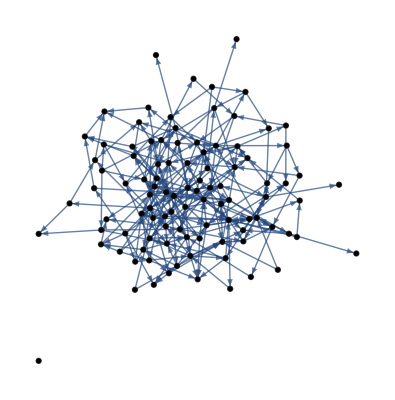

```mathematica
RandomGraph[{100,250},DirectedEdges->True,VertexStyle->Black]
```

```mathematica
<<"IGraphM`"
```

IGraph/M 0.4 (April 2, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
f[x_,n_,k_,p_]=x^n/(k^n+x^n)(p(p+1))/2+k^n/(k^n+x^n)((p-1)p)/2+(p+1)(1-p);
```

```mathematica
MFLC={Graph[EdgeList[#[[1]]],EdgeStyle->Thread[EdgeList[#[[1]]]->(If[#==-1,Red,Blue]&/@#[[2,2]])],VertexLabels->"Name"],#}&/@Gather[{Graph[{x->y,y->x},DirectedEdges->True],"EdgeColors"->#}&/@Flatten[Outer[List,##]&@@Array[{-1,1}&,2],1],IGVF2IsomorphicQ[#1,#2]&][[;;,1]];
```

```mathematica
MFLCAR={Graph[Join[EdgeList[#[[1]]],{x->x,y->y}],EdgeStyle->Thread[EdgeList[#[[1]]]->(If[#==-1,Red,Blue]&/@#[[2,2]])],VertexLabels->"Name"],#}&/@Gather[{Graph[{x->y,y->x},DirectedEdges->True],"EdgeColors"->#}&/@Flatten[Outer[List,##]&@@Array[{-1,1}&,2],1],IGVF2IsomorphicQ[#1,#2]&][[;;,1]];
```

Figure 3B:

```mathematica
DynamicModule[{kxx=0.01,kxy=0.3,kyx=0.3,kyy=0.01,nxx=1,nxy=3,nyx=3,nyy=1,tmax=10,x0=0,y0=0},{MFLC⟦1,1⟧,Show[StreamPlot[({f[y,nyx,kyx,#1⟦2⟧]-x,f[x,nxy,kxy,#1⟦1⟧]-y}&)[MFLC⟦1,2,2,2⟧],{x,0,1},{y,0,1},PlotRange->All],ContourPlot[Evaluate[({f[y,nyx,kyx,#1⟦2⟧]-x==0,f[x,nxy,kxy,#1⟦1⟧]-y==0}&)[MFLC⟦1,2,2,2⟧]],{x,0,1},{y,0,1},PlotRange->All]]}]
```

Figure 3C:

```mathematica
DynamicModule[{kxx=0.01,kxy=0.3,kyx=0.3,kyy=0.01,nxx=1,nxy=3,nyx=3,nyy=1,tmax=10,x0=0,y0=0},{MFLC⟦3,1⟧,Show[StreamPlot[({f[y,nyx,kyx,#1⟦2⟧]-x,f[x,nxy,kxy,#1⟦1⟧]-y}&)[MFLC⟦3,2,2,2⟧],{x,0,1},{y,0,1},PlotRange->All],ContourPlot[Evaluate[({f[y,nyx,kyx,#1⟦2⟧]-x==0,f[x,nxy,kxy,#1⟦1⟧]-y==0}&)[MFLC⟦3,2,2,2⟧]],{x,0,1},{y,0,1},PlotRange->All]]}]
```

Figure 3D:

```mathematica
DynamicModule[{kxx=0.01,kxy=0.3,kyx=0.3,kyy=0.01,nxx=1,nxy=3,nyx=3,nyy=1,tmax=10,x0=0,y0=0},{MFLC⟦2,1⟧,Show[StreamPlot[({f[y,nyx,kyx,#1⟦2⟧]-x,f[x,nxy,kxy,#1⟦1⟧]-y}&)[MFLC⟦2,2,2,2⟧],{x,0,1},{y,0,1},PlotRange->All],ContourPlot[Evaluate[({f[y,nyx,kyx,#1⟦2⟧]-x==0,f[x,nxy,kxy,#1⟦1⟧]-y==0}&)[MFLC⟦2,2,2,2⟧]],{x,0,1},{y,0,1},PlotRange->All]]}]
```

Figure 3G:

```mathematica
DynamicModule[{kxx=0.3,kxy=0.3,kyx=0.3,kyy=0.3,nxx=3,nxy=3,nyx=3,nyy=3,tmax=10,x0=0,y0=0},{MFLCAR⟦1,1⟧,Show[StreamPlot[({f[y,nyx,kyx,#1⟦2⟧]f[x,nxx,kxx,1]-x,f[x,nxy,kxy,#1⟦1⟧]f[y,nyy,kyy,1]-y}&)[MFLC⟦1,2,2,2⟧],{x,0,1},{y,0,1},PlotRange->All],ContourPlot[Evaluate[({f[y,nyx,kyx,#1⟦2⟧]f[x,nxx,kxx,1]-x==0,f[x,nxy,kxy,#1⟦1⟧]f[y,nyy,kyy,1]-y==0}&)[MFLC⟦1,2,2,2⟧]],{x,0,1},{y,0,1},PlotRange->All]]}]
```

Figure 3H:

```mathematica
DynamicModule[{kxx=0.2,kxy=0.3,kyx=0.3,kyy=0.2,nxx=3,nxy=3,nyx=3,nyy=3,tmax=10,x0=0,y0=0},{MFLCAR⟦2,1⟧,Show[StreamPlot[({f[y,nyx,kyx,#1⟦2⟧]f[x,nxx,kxx,1]-x,f[x,nxy,kxy,#1⟦1⟧]f[y,nyy,kyy,1]-y}&)[MFLC⟦2,2,2,2⟧],{x,0,1},{y,0,1},PlotRange->All],ContourPlot[Evaluate[({f[y,nyx,kyx,#1⟦2⟧]f[x,nxx,kxx,1]-x==0,f[x,nxy,kxy,#1⟦1⟧]f[y,nyy,kyy,1]-y==0}&)[MFLC⟦2,2,2,2⟧]],{x,0,1},{y,0,1},PlotRange->All]]}]
```

Figure 3I:

```mathematica
CFFL[a_,b_,c_]:=ParametricNDSolveValue[{x'[t]==f[x[t],nxx,kxx,a]-x[t],
y'[t]==f[y[t],nyy,kyy,b]f[x[t],nxy,kxy,1]-y[t],
z'[t]==f[z[t],nzz,kzz,c]f[x[t],nxz,kxz,1]f[y[t],nyz,kyz,1]-z[t],x[0]==x0,y[0]==y0,z[0]==z0},{x[t],y[t],z[t]},{t,0,100},{kxx,kyy,kzz,kxy,kxz,kyz,nxx,nyy,nzz,nxy,nxz,nyz,x0,y0,z0}];
```

```mathematica
Table[DynamicModule[{kxx=0.3,kxy=0.01,kxz=0.01,kyy=0.3,kyz=0.01,kzz=0.3,nxx=3,nxy=1,nxz=1,nyy=3,nyz=1,nzz=3,tmax=10,x0=a,y0=0.185,z0=0.19},Show[Plot[Evaluate[CFFL[#1⟦1,1⟧,#1⟦1,2⟧,#1⟦1,3⟧][kxx,kyy,kzz,kxy,kxz,kyz,nxx,nyy,nzz,nxy,nxz,nyz,x0,y0,z0]]⟦3⟧/.t->t1,{t1,0,tmax},PlotRange->All,PlotStyle->{Thick,#1⟦2⟧},AxesOrigin->{0,0}]&/@Transpose[{Select[SortBy[Flatten[(Outer[List,##1]&)@@Array[{-1,0,1}&,3],2],-Count[#1,0]&],Count[#1,-1]==0&][[;;4]],{Black,Blue,Red,Gray}}]]],{a,{0,.1,.5}}]
```

{,,}

Figure 3J:

```mathematica
IFFL[a_,b_,c_]:=ParametricNDSolveValue[{x'[t]==f[x[t],nxx,kxx,a]-x[t],
y'[t]==f[y[t],nyy,kyy,b]f[x[t],nxy,kxy,1]-y[t],
z'[t]==f[z[t],nzz,kzz,c]f[x[t],nxz,kxz,1]f[y[t],nyz,kyz,-1]-z[t],x[0]==x0,y[0]==y0,z[0]==z0},{x[t],y[t],z[t]},{t,0,100},{kxx,kyy,kzz,kxy,kxz,kyz,nxx,nyy,nzz,nxy,nxz,nyz,x0,y0,z0}];
```

```mathematica
Table[DynamicModule[{kxx=0.3,kxy=0.01,kxz=0.01,kyy=0.3,kyz=(*0.1*).5,kzz=(*0.3*)0.15,nxx=3,nxy=1,nxz=1,nyy=3,nyz=1,nzz=3,tmax=10,x0=a,y0=0.185,z0=0.19},Show[Plot[Evaluate[IFFL[#1⟦1,1⟧,#1⟦1,2⟧,#1⟦1,3⟧][kxx,kyy,kzz,kxy,kxz,kyz,nxx,nyy,nzz,nxy,nxz,nyz,x0,y0,z0]]⟦3⟧/.t->t1,{t1,0,tmax},PlotRange->{All,{0,1}},PlotStyle->{Thick,#1⟦2⟧},AxesOrigin->{0,0}]&/@Transpose[{Select[SortBy[Flatten[(Outer[List,##1]&)@@Array[{-1,0,1}&,3],2],-Count[#1,0]&],Count[#1,-1]==0&][[;;4]],{Black,Blue,Red,Gray}}]]],{a,{0,.1,.5}}]
```

{,,}

Figure 3K-M:

```mathematica
MFLMFLC={Graph[EdgeList[#[[1]]],EdgeStyle->Thread[EdgeList[#[[1]]]->(If[#==-1,Red,Blue]&/@#[[2,2]])],VertexLabels->"Name"],#}&/@Gather[{Graph[{x->y,y->x,y->z,z->y},DirectedEdges->True],"EdgeColors"->#}&/@Flatten[Outer[List,##]&@@Array[{-1,1}&,4],3],IGVF2IsomorphicQ[#1,#2]&][[;;,1]];
```

```mathematica
MFLMFLeqs[a_,b_,c_,circ_]:=
ParametricNDSolveValue[{x'[t]==f[x[t],nxx,kxx,a]f[y[t],nyx,kyx,circ[[2]]]-x[t],
y'[t]==f[y[t],nyy,kyy,b]f[x[t],nxy,kxy,circ[[1]]]f[z[t],nzy,kzy,circ[[4]]]-y[t],
z'[t]==f[z[t],nzz,kzz,c]f[y[t],nyz,kyz,circ[[3]]]-z[t],x[0]==x0,y[0]==y0,z[0]==z0},{x[t],y[t],z[t]},{t,0,100},{kxx,kyy,kzz,kyx,kxy,kzy,kyz,nxx,nyy,nzz,nyx,nxy,nzy,nyz,x0,y0,z0(*,τx,τy,τz*)}];
```

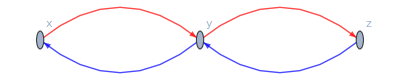

```mathematica
{MFLMFLC[[5,1]],Manipulate[Table[Plot[Evaluate@MFLMFLeqs[1,1,1,MFLMFLC[[5,2,2,2]]][kxx,kyy,kzz,kyx,kxy,kzy,kyz,nxx,nyy,nzz,nyx,nxy,nzy,nyz,a,y0,z0],{t,0,tmax},PlotRange->All,PlotLegends->{x,y,z},PlotStyle->{Black,Red,Blue}],{a,{0,0.1,0.2,0.4,0.6,0.7}}],
{{kxx,.2},.01,100},{{kyy,.2},.01,100},{{kzz,.2},.01,100},{{kyx,.3},.01,100},{{kxy,.3},.01,100},{{kzy,.3},.01,100},{{kyz,.3},.01,100},{{nxx,3},{1,2,3,4}},{{nyy,3},{1,2,3,4}},{{nzz,3},{1,2,3,4}},{{nyx,3},{1,2,3,4}},{{nxy,3},{1,2,3,4}},{{nzy,3},{1,2,3,4}},{{nyz,3},{1,2,3,4}},{{y0,.2},0,10},{{z0,.2},0,10},{{tmax,10},10,100}]}
```

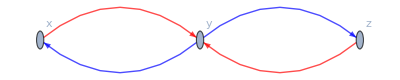

```mathematica
{MFLMFLC[[6,1]],Manipulate[Table[Plot[Evaluate@MFLMFLeqs[1,1,1,MFLMFLC[[6,2,2,2]]][kxx,kyy,kzz,kyx,kxy,kzy,kyz,nxx,nyy,nzz,nyx,nxy,nzy,nyz,a,y0,z0],{t,0,tmax},PlotRange->All,PlotLegends->{x,y,z},PlotStyle->{Black,Red,Blue}],{a,{0,0.1,0.2,0.4,0.6,0.7}}],
{{kxx,.2},.01,100},{{kyy,.2},.01,100},{{kzz,.2},.01,100},{{kyx,.3},.01,100},{{kxy,.3},.01,100},{{kzy,.3},.01,100},{{kyz,.3},.01,100},{{nxx,3},{1,2,3,4}},{{nyy,3},{1,2,3,4}},{{nzz,3},{1,2,3,4}},{{nyx,3},{1,2,3,4}},{{nxy,3},{1,2,3,4}},{{nzy,3},{1,2,3,4}},{{nyz,3},{1,2,3,4}},{{y0,.2},0,10},{{z0,.2},0,10},{{tmax,10},10,100}]}
```

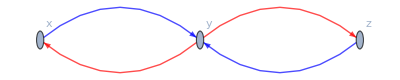

```mathematica
{MFLMFLC[[8,1]],Manipulate[Table[Plot[Evaluate@MFLMFLeqs[1,1,1,MFLMFLC[[8,2,2,2]]][kxx,kyy,kzz,kyx,kxy,kzy,kyz,nxx,nyy,nzz,nyx,nxy,nzy,nyz,x0,a,z0],{t,0,tmax},PlotRange->All,PlotLegends->{x,y,z},PlotStyle->{Red,Black,Blue}],{a,{0,0.1,0.2,0.4,0.6,0.7}}],
{{kxx,.2},.01,100},{{kyy,.2},.01,100},{{kzz,.2},.01,100},{{kyx,.3},.01,100},{{kxy,.3},.01,100},{{kzy,.3},.01,100},{{kyz,.3},.01,100},{{nxx,3},{1,2,3,4}},{{nyy,3},{1,2,3,4}},{{nzz,3},{1,2,3,4}},{{nyx,3},{1,2,3,4}},{{nxy,3},{1,2,3,4}},{{nzy,3},{1,2,3,4}},{{nyz,3},{1,2,3,4}},{{x0,.18},0,10},{{z0,.2},0,10},{{tmax,10},10,100}]}
```

Figure 3N-O:

```mathematica
MFLFFLMedeqs[a_,b_,c_,d_,circ_]:=
ParametricNDSolveValue[{x'[t]==f[x[t],nxx,kxx,a]-x[t],
y'[t]==f[x[t],nxy,kxy,circ[[1]]]f[y[t],nyy,kyy,b]f[w[t],nwy,kwy,circ[[5]]]-y[t],
z'[t]==f[z[t],nzz,kzz,c]f[y[t],nyz,kyz,circ[[2]]]f[x[t],nxz,kxz,circ[[3]]]-z[t],
w'[t]==f[w[t],nww,kww,d]f[y[t],nyw,kyw,circ[[4]]]-w[t],x[0]==x0,y[0]==y0,z[0]==z0,w[0]==w0},{x[t],y[t],z[t],w[t]},{t,0,100},{kxx,kyy,kzz,kww,kwy,kyw,kxy,kxz,kyz,nxx,nyy,nzz,nww,nwy,nyw,nxy,nxz,nyz,x0,y0,z0,w0}];
```

```mathematica
MFLFFLMedC={Graph[EdgeList[#[[1]]],EdgeStyle->Thread[EdgeList[#[[1]]]->(If[#==-1,Red,Blue]&/@#[[2,2]])],VertexLabels->"Name"],#}&/@Gather[{Graph[{x->y,y->z,x->z,y->w,w->y},DirectedEdges->True],"EdgeColors"->#}&/@Flatten[Outer[List,##]&@@Array[{-1,1}&,5],4],IGVF2IsomorphicQ[#1,#2]&][[;;,1]];
```

```mathematica
Table[DynamicModule[{kww=0.2,kwy=0.3,kxx=0.3,kxy=0.01,kxz=0.01,kyw=0.3,kyy=0.2,kyz=0.01,kzz=0.01,nww=3,nwy=3,nxx=3,nxy=1,nxz=1,nyw=3,nyy=3,nyz=3,nzz=1,tmax=20,w0=a,x0=0.01,y0=0.3,z0=0.01},Plot[Evaluate[MFLFFLMedeqs[0,1,0,1,MFLFFLMedC⟦-3,2,2,2⟧][kxx,kyy,kzz,kww,kwy,kyw,kxy,kxz,kyz,nxx,nyy,nzz,nww,nwy,nyw,nxy,nxz,nyz,x0,y0,z0,w0]⟦3⟧],{t,0.01,tmax},PlotRange->{All,{0,1}},PlotStyle->Black]],{a,{0.1,1,10}}]
```

{,,}

```mathematica
Table[DynamicModule[{kww=0.2,kwy=0.3,kxx=0.3,kxy=0.01,kxz=0.01,kyw=0.3,kyy=0.2,kyz=0.5,kzz=0.01,nww=3,nwy=3,nxx=3,nxy=1,nxz=1,nyw=3,nyy=3,nyz=1,nzz=1,tmax=20,w0=a,x0=0.01,y0=0.3,z0=0.01},Plot[Evaluate[MFLFFLMedeqs[0,1,0,1,MFLFFLMedC⟦22,2,2,2⟧][kxx,kyy,kzz,kww,kwy,kyw,kxy,kxz,kyz,nxx,nyy,nzz,nww,nwy,nyw,nxy,nxz,nyz,x0,y0,z0,w0]⟦3⟧],{t,0.01,tmax},PlotRange->{All,{0,1}},PlotStyle->Black]],{a,{0.1,1,10}}]
```

{,,}

Figure 4A:

```mathematica
ceCirc4C1=ParametricNDSolveValue[{
x'[t]==f[y[t],nyx,kyx,pyx]-x[t],
y'[t]==f[x[t],nxy,kxy,pxy]f[z[t],nzy,kzy,pzy]-y[t],
z'[t]==f[x[t],nxz,kxz,pxz]f[y[t],nyz,kyz,pyz]-z[t],
x[0]==x0,y[0]==y0,z[0]==z0},{x[t],y[t],z[t]},{t,0,100},{nyx,nxy,nzy,nxz,nyz,kyx,kxy,kzy,kxz,kyz,pyx,pxy,pzy,pxz,pyz,x0,y0,z0}];
```

```mathematica
ceCirc4=ParametricNDSolveValue[{
x'[t]==f[y[t],nyx,kyx,pyx]f[w[t],nwx,kwx,pwx]-x[t],
y'[t]==f[x[t],nxy,kxy,pxy]f[z[t],nzy,kzy,pzy]-y[t],
z'[t]==f[x[t],nxz,kxz,pxz]f[y[t],nyz,kyz,pyz]f[w[t],nwz,kwz,pwz]-z[t],
w'[t]==f[x[t],nxw,kxw,pxw]f[z[t],nzw,kzw,pzw]-w[t],
x[0]==x0,y[0]==y0,z[0]==z0,w[0]==w0},{x[t],y[t],z[t],w[t]},{t,0,100},{nyx,nwx,nxy,nzy,nxz,nyz,nwz,nxw,nzw,kyx,kwx,kxy,kzy,kxz,kyz,kwz,kxw,kzw,pyx,pwx,pxy,pzy,pxz,pyz,pwz,pxw,pzw,x0,y0,z0,w0}];
```

```mathematica
DynamicModule[{kwx=0.01,kwz=3.38,kxw=0.01,kxy=0.01,kxz=0.01,kyx=0.01,kyz=0.01,kzw=0.16,kzy=0.01,nwx=3,nwz=3,nxw=3,nxy=3,nxz=3,nyx=3,nyz=3,nzw=3,nzy=3,pwx=1,pwz=1,pxw=1,pxy=1,pxz=1,pyx=1,pyz=1,pzw=1,pzy=1,tmax=17.9,w0=0.668,x0=0.618,y0=0.64,z0=0.64},Show[{Plot[Evaluate[ceCirc4C1[nyx,nxy,nzy,nxz,nyz,kyx,kxy,kzy,kxz,kyz,pyx,pxy,pzy,pxz,pyz,x0,y0,z0][[2]]],{t,0,tmax},PlotRange->All,PlotStyle->Red],Plot[Evaluate[ceCirc4[nyx,nwx,nxy,nzy,nxz,nyz,nwz,nxw,nzw,kyx,kwx,kxy,kzy,kxz,kyz,kwz,kxw,kzw,pyx,pwx,pxy,pzy,pxz,pyz,pwz,pxw,pzw,x0,y0,z0,w0]],{t,0,tmax},PlotRange->All,PlotLegends->{x,y,z,w},PlotStyle->{Black,Red,{Black,Dashed},{Red,Dashed}}]},AxesOrigin->{0,0}]]
```

Figure 4B:

```mathematica
DynamicModule[{kwx=0.01,kwz=0.01,kxw=0.01,kxy=0.01,kxz=0.01,kyx=1.87,kyz=0.01,kzw=0.01,kzy=0.01,nwx=3,nwz=3,nxw=3,nxy=3,nxz=3,nyx=3,nyz=3,nzw=3,nzy=3,pwx=1,pwz=1,pxw=1,pxy=1,pxz=-1,pyx=1,pyz=1,pzw=1,pzy=1,tmax=47.6,w0=0.08600000000000001,x0=0.,y0=0.654,z0=0.},Show[Plot[Evaluate[ceCirc4[nyx,nwx,nxy,nzy,nxz,nyz,nwz,nxw,nzw,kyx,kwx,kxy,kzy,kxz,kyz,kwz,kxw,kzw,pyx,pwx,pxy,pzy,pxz,pyz,pwz,pxw,pzw,x0,y0,z0,w0][[{2,4}]]],{t,0,tmax},PlotRange->All,PlotLegends->{y,w},PlotStyle->{Black,Red}],Plot[Evaluate[ceCirc4C1[nwx,nxw,nzw,nxz,nwz,kwx,kxw,kzw,kxz,kwz,pwx,pxw,pzw,pxz,pwz,x0,w0,z0]][[2]],{t,0,tmax},PlotRange->All,PlotStyle->Red],AxesOrigin->{0,0}]]
```

Figure 4C-D:

```mathematica
E3Circ3Loop=ParametricNDSolveValue[{
x'[t]==f[z[t],nzx,kzx,pzx]-x[t],
y'[t]==f[x[t],nxy,kxy,pxy]-y[t],
z'[t]==f[y[t],nyz,kyz,pyz]-z[t],
x[0]==x0,y[0]==y0,z[0]==z0},{x[t],y[t],z[t]},{t,0,100},{kzx,kxy,kyz,nzx,nxy,nyz,pzx,pxy,pyz,x0,y0,z0}];
```

```mathematica
E3Circ1=ParametricNDSolveValue[{
x'[t]==f[z[t],nzx,kzx,pzx]f[w[t],nwx,kwx,pwx]-x[t],
y'[t]==f[x[t],nxy,kxy,pxy]-y[t],
z'[t]==f[y[t],nyz,kyz,pyz]-z[t],
w'[t]==f[y[t],nyw,kyw,pyw]-w[t],
x[0]==x0,y[0]==y0,z[0]==z0,w[0]==w0},{x[t],y[t],z[t],w[t]},{t,0,100},{kzx,kwx,kxy,kyz,kyw,nzx,nwx,nxy,nyz,nyw,pzx,pwx,pxy,pyz,pyw,x0,y0,z0,w0}];
```

```mathematica
DynamicModule[{kwx=0.01,kxy=0.01,kyw=0.01,kyz=0.01,kzx=4.7,nwx=3,nxy=3,nyw=3,nyz=3,nzx=3,pwx=1,pxy=1,pyw=1,pyz=-1,pzx=1,tmax=51.,w0=0,x0=0.1,y0=0,z0=(*0.066*)0},{Plot[Evaluate[E3Circ1[kzx,kwx,kxy,kyz,kyw,nzx,nwx,nxy,nyz,nyw,pzx,pwx,pxy,pyz,pyw,x0,y0,z0,w0][[3;;]]],{t,0,tmax},PlotRange->All,PlotLegends->{z,w},PlotStyle->{{Black,Thick},{Red,Thick}}],
Plot[Evaluate[E3Circ3Loop[kzx,kxy,kyz,nzx,nxy,nyz,pzx,pxy,pyz,x0,y0,z0][[3]]],{t,0,tmax},PlotRange->All,PlotStyle->{Thick,Black}],
Plot[Evaluate[E3Circ3Loop[kwx,kxy,kyw,nwx,nxy,nyw,pwx,pxy,pyw,x0,y0,w0][[3]]],{t,0,tmax},PlotRange->All,PlotStyle->{Red,Thick}]}]
```

Figure 5A:

```mathematica
gPlotMFLMFL1[{pxx_,pyy_,pzz_,puu_,pyx_,pxy_,pzx_,puz_,pzu_,pyu_}]:=Module[{edges,edgeStyle},
edges=DeleteCases[{Abs[pxx](x->x),Abs[pyy](y->y),Abs[pzz](z->z),Abs[puu](u->u),Abs[pyx](y->x),Abs[pxy](x->y),Abs[pzx](z->x),Abs[puz](u->z),Abs[pzu](z->u),Abs[pyu](y->u)},0];
edgeStyle=Thread[edges->Select[{pxx,pyy,pzz,puu,pyx,pxy,pzx,puz,pzu,pyu},#≠ 0&]]/.{1->Blue,-1->Red};
Graph[edges,VertexLabels->"Name",EdgeStyle->edgeStyle]]
```

```mathematica
MFLMFL1ST[kxx_,kyy_,kzz_,kuu_,kyx_,kxy_,kzx_,kuz_,kzu_,kyu_,nxx_,nyy_,nzz_,nuu_,nyx_,nxy_,nzx_,nuz_,nzu_,nyu_,pxx_,pyy_,pzz_,puu_,pyx_,pxy_,pzx_,puz_,pzu_,pyu_]:=Module[{stst,egs},
stst=Union[Thread[#[[;;,1]]->Round[#[[;;,2]],.01]]&/@Select[NSolve[{0==f[x,nxx,kxx,pxx]f[y,nyx,kyx,pyx]f[z,nzx,kzx,pzx]-x,
0==f[y,nyy,kyy,pyy]f[x,nxy,kxy,pxy]-y,
0==f[z,nzz,kzz,pzz]f[u,nuz,kuz,puz]-z,
0==f[u,nuu,kuu,puu]f[z,nzu,kzu,pzu]f[y,nyu,kyu,pyu]-u},{x,y,z,u}],And@@(NonNegative[#]&/@#[[;;,2]])&]];
egs=Eigenvalues[#]&/@(D[{f[x,nxx,kxx,pxx]f[y,nyx,kyx,pyx]f[z,nzx,kzx,pzx]-x,
f[y,nyy,kyy,pyy]f[x,nxy,kxy,pxy]-y,
f[z,nzz,kzz,pzz]f[u,nuz,kuz,puz]-z,
f[u,nuu,kuu,puu]f[z,nzu,kzu,pzu]f[y,nyu,kyu,pyu]-u},{{x,y,z,u}}]/.stst);
{stst,egs}ᵀ];
```

```mathematica
Table[DynamicModule[{kuu=0.2,kuz=0.3,kxx=0.2,kxy=0.3,kyu=0.01,kyx=0.3,kyy=0.2,kzu=0.3,kzx=0.01,kzz=0.2,nuu=3,nuz=3,nxx=3,nxy=3,nyu=1,nyx=3,nyy=3,nzu=3,nzx=1,nzz=3},{gPlotMFLMFL1[{1,1,1,1,p[[1]],p[[2]],p[[3]],p[[4]],p[[5]],p[[6]]}],ArrayPlot[{x,y,z,u}/.(Select[#,And@@(Re[#]<0&/@#[[2]])&][[;;,1]]&@MFLMFL1ST[kxx,kyy,kzz,kuu,kyx,kxy,kzx,kuz,kzu,kyu,nxx,nyy,nzz,nuu,nyx,nxy,nzx,nuz,nzu,nyu,1,1,1,1,p[[1]],p[[2]],p[[3]],p[[4]],p[[5]],p[[6]]])]}],{p,{{-1,1,-1,1,-1,-1},{1,-1,-1,-1,1,-1},{-1,1,-1,-1,1,-1}}}]
```

{,,}

Figure 5B:

```mathematica
Table[DynamicModule[{kuu=0.2,kuz=0.3,kxx=0.2,kxy=0.3,kyu=0.01,kyx=0.3,kyy=0.2,kzu=0.3,kzx=0.01,kzz=0.2,nuu=3,nuz=3,nxx=3,nxy=3,nyu=1,nyx=3,nyy=3,nzu=3,nzx=1,nzz=3},{gPlotMFLMFL1[{1,1,1,1,p[[1]],p[[2]],p[[3]],p[[4]],p[[5]],p[[6]]}],ArrayPlot[{x,y,z,u}/.(Select[#,And@@(Re[#]<0&/@#[[2]])&][[;;,1]]&@MFLMFL1ST[kxx,kyy,kzz,kuu,kyx,kxy,kzx,kuz,kzu,kyu,nxx,nyy,nzz,nuu,nyx,nxy,nzx,nuz,nzu,nyu,1,1,1,1,p[[1]],p[[2]],p[[3]],p[[4]],p[[5]],p[[6]]])]}],{p,{{-1,1,1,1,-1,1},{1,-1,1,-1,1,1},{-1,1,1,-1,1,1}}}]
```

{,,}

Figure 5C:

```mathematica
gPlot2[{pxx_,pyy_,pzz_,puu_,pvv_,pvx_,pxy_,pxz_,pyz_,pzu_,pvu_,puv_}]:=Module[{edges,edgeStyle},
edges=DeleteCases[{Abs[pxx](x->x),Abs[pyy](y->y),Abs[pzz](z->z),Abs[puu](u->u),Abs[pvv](v->v),Abs[pvx](v->x),Abs[pxy](x->y),Abs[pxz](x->z),Abs[pyz](y->z),Abs[pzu](z->u),Abs[pvu](v->u),Abs[puv](u->v)},0];
edgeStyle=Thread[edges->Select[{pxx,pyy,pzz,puu,pvv,pvx,pxy,pxz,pyz,pzu,pvu,puv},#≠ 0&]]/.{1->Blue,-1->Red};
Graph[edges,VertexLabels->"Name",EdgeStyle->edgeStyle]]
```

```mathematica
FFLMLIntAND2=ParametricNDSolveValue[{x'[t]==f[x[t],nxx,kxx,pxx]f[v[t],nvx,kvx,pvx]-x[t],
y'[t]==f[y[t],nyy,kyy,pyy]f[x[t],nxy,kxy,pxy]-y[t],
z'[t]==f[z[t],nzz,kzz,pzz]f[y[t],nyz,kyz,pyz]f[x[t],nxz,kxz,pxz]-z[t],
u'[t]==f[z[t],nzu,kzu,pzu]f[u[t],nuu,kuu,puu]f[v[t],nvu,kvu,pvu]-u[t],
v'[t]==f[u[t],nuv,kuv,puv]f[v[t],nvv,kvv,pvv]-v[t],x[0]==x0,y[0]==y0,z[0]==z0,u[0]==u0,v[0]==v0},{x[t],y[t],z[t],u[t],v[t]},{t,0,100},{kxx,kyy,kzz,kuu,kvv,kvx,kxy,kxz,kyz,kzu,kvu,kuv,nxx,nyy,nzz,nuu,nvv,nvx,nxy,nxz,nyz,nzu,nvu,nuv,pxx,pyy,pzz,puu,pvv,pvx,pxy,pxz,pyz,pzu,pvu,puv,x0,y0,z0,u0,v0}];
```

```mathematica
DynamicModule[{kuu=0.3,kuv=0.3,kvu=0.3,kvv=0.3,kvx=0.01,kxx=0.3,kxy=0.01,kxz=0.01,kyy=0.3,kyz=0.01,kzu=0.01,kzz=0.3,nuu=1,nuv=3,nvu=3,nvv=1,nvx=1,nxx=3,nxy=1,nxz=1,nyy=3,nyz=1,nzu=1,nzz=3,tmax=86.60000000000001,u0=0.5,v0=0.6,x0=0.,y0=0.,z0=0.},{gPlot2[{0,0,0,1,1,{1,1,1,1,1,-1,-1}⟦1⟧,{1,1,1,1,1,-1,-1}⟦2⟧,{1,1,1,1,1,-1,-1}⟦3⟧,{1,1,1,1,1,-1,-1}⟦4⟧,{1,1,1,1,1,-1,-1}⟦5⟧,{1,1,1,1,1,-1,-1}⟦6⟧,{1,1,1,1,1,-1,-1}⟦7⟧}],Plot[Evaluate[FFLMLIntAND2[kxx,kyy,kzz,kuu,kvv,kvx,kxy,kxz,kyz,kzu,kvu,kuv,nxx,nyy,nzz,nuu,nvv,nvx,nxy,nxz,nyz,nzu,nvu,nuv,0,0,0,1,1,{1,1,1,1,1,-1,-1}⟦1⟧,{1,1,1,1,1,-1,-1}⟦2⟧,{1,1,1,1,1,-1,-1}⟦3⟧,{1,1,1,1,1,-1,-1}⟦4⟧,{1,1,1,1,1,-1,-1}⟦5⟧,{1,1,1,1,1,-1,-1}⟦6⟧,{1,1,1,1,1,-1,-1}⟦7⟧,x0,y0,z0,u0,v0]⟦1;;3⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{x,y,z},AxesOrigin->{0,0},PlotStyle->{{Thick,Black},{Thick,Gray},{Red,Thick}}],Plot[Evaluate[FFLMLIntAND2[kxx,kyy,kzz,kuu,kvv,kvx,kxy,kxz,kyz,kzu,kvu,kuv,nxx,nyy,nzz,nuu,nvv,nvx,nxy,nxz,nyz,nzu,nvu,nuv,0,0,0,1,1,{1,1,1,1,1,-1,-1}⟦1⟧,{1,1,1,1,1,-1,-1}⟦2⟧,{1,1,1,1,1,-1,-1}⟦3⟧,{1,1,1,1,1,-1,-1}⟦4⟧,{1,1,1,1,1,-1,-1}⟦5⟧,{1,1,1,1,1,-1,-1}⟦6⟧,{1,1,1,1,1,-1,-1}⟦7⟧,x0,y0,z0,u0,v0]⟦4;;All⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{u,v},AxesOrigin->{0,0},PlotStyle->{{Thick,Dashed,Black},{Thick,Dashed,Red}}]}]
```

```mathematica
DynamicModule[{kuu=0.3,kuv=0.3,kvu=0.3,kvv=0.3,kvx=0.01,kxx=0.3,kxy=0.01,kxz=0.01,kyy=0.3,kyz=0.01,kzu=0.01,kzz=0.3,nuu=1,nuv=3,nvu=3,nvv=1,nvx=1,nxx=3,nxy=1,nxz=1,nyy=3,nyz=1,nzu=1,nzz=3,tmax=86.60000000000001,u0=0.5,v0=0.4,x0=0.,y0=0.,z0=0.},{gPlot2[{0,0,0,1,1,{1,1,1,1,1,-1,-1}⟦1⟧,{1,1,1,1,1,-1,-1}⟦2⟧,{1,1,1,1,1,-1,-1}⟦3⟧,{1,1,1,1,1,-1,-1}⟦4⟧,{1,1,1,1,1,-1,-1}⟦5⟧,{1,1,1,1,1,-1,-1}⟦6⟧,{1,1,1,1,1,-1,-1}⟦7⟧}],Plot[Evaluate[FFLMLIntAND2[kxx,kyy,kzz,kuu,kvv,kvx,kxy,kxz,kyz,kzu,kvu,kuv,nxx,nyy,nzz,nuu,nvv,nvx,nxy,nxz,nyz,nzu,nvu,nuv,0,0,0,1,1,{1,1,1,1,1,-1,-1}⟦1⟧,{1,1,1,1,1,-1,-1}⟦2⟧,{1,1,1,1,1,-1,-1}⟦3⟧,{1,1,1,1,1,-1,-1}⟦4⟧,{1,1,1,1,1,-1,-1}⟦5⟧,{1,1,1,1,1,-1,-1}⟦6⟧,{1,1,1,1,1,-1,-1}⟦7⟧,x0,y0,z0,u0,v0]⟦1;;3⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{x,y,z},AxesOrigin->{0,0},PlotStyle->{{Thick,Black},{Thick,Gray},{Red,Thick}}],Plot[Evaluate[FFLMLIntAND2[kxx,kyy,kzz,kuu,kvv,kvx,kxy,kxz,kyz,kzu,kvu,kuv,nxx,nyy,nzz,nuu,nvv,nvx,nxy,nxz,nyz,nzu,nvu,nuv,0,0,0,1,1,{1,1,1,1,1,-1,-1}⟦1⟧,{1,1,1,1,1,-1,-1}⟦2⟧,{1,1,1,1,1,-1,-1}⟦3⟧,{1,1,1,1,1,-1,-1}⟦4⟧,{1,1,1,1,1,-1,-1}⟦5⟧,{1,1,1,1,1,-1,-1}⟦6⟧,{1,1,1,1,1,-1,-1}⟦7⟧,x0,y0,z0,u0,v0]⟦4;;All⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{u,v},AxesOrigin->{0,0},PlotStyle->{{Thick,Dashed,Black},{Thick,Dashed,Red}}]}]
```

Figure 5D:

```mathematica
FFLFFL=ParametricNDSolveValue[{x'[t]==f[x[t],nxx,kxx,pxx]f[u[t],nux,kux,pux]-x[t],
y'[t]==f[y[t],nyy,kyy,pyy]f[x[t],nxy,kxy,pxy]-y[t],
z'[t]==f[z[t],nzz,kzz,pzz]f[y[t],nyz,kyz,pyz]f[x[t],nxz,kxz,pxz]-z[t],
w'[t]==f[w[t],nww,kww,pww]f[z[t],nzw,kzw,pzw]-w[t],
v'[t]==f[w[t],nwv,kwv,pwv]f[v[t],nvv,kvv,pvv]-v[t],
u'[t]==f[w[t],nwu,kwu,pwu]f[u[t],nuu,kuu,puu]f[v[t],nvu,kvu,pvu]-u[t],x[0]==x0,y[0]==y0,z[0]==z0,w[0]==w0,u[0]==u0,v[0]==v0},{x[t],y[t],z[t],w[t],v[t],u[t]},{t,0,100},{kxx,kyy,kzz,kww,kuu,kvv,kux,kxy,kyz,kxz,kzw,kwv,kwu,kvu,nxx,nyy,nzz,nww,nuu,nvv,nux,nxy,nyz,nxz,nzw,nwv,nwu,nvu,pxx,pyy,pzz,pww,puu,pvv,pux,pxy,pyz,pxz,pzw,pwv,pwu,pvu,x0,y0,z0,w0,u0,v0}];
```

```mathematica
DynamicModule[{kuu=0.3,kux=0.01,kvu=13.4,kvv=0.3,kwu=55.900000000000006,kwv=70.8,kww=0.3,kxx=0.3,kxy=0.01,kxz=0.01,kyy=0.3,kyz=0.01,kzw=0.01,kzz=0.3,nuu=1,nux=1,nvu=1,nvv=1,nwu=1,nwv=1,nww=1,nxx=1,nxy=1,nxz=1,nyy=1,nyz=1,nzw=1,nzz=1,tmax=45.6,u0=0.01,v0=0.01,w0=0.01,x0=0.01,y0=0.01,z0=0.01},{Plot[Evaluate[FFLFFL[kxx,kyy,kzz,kww,kuu,kvv,kux,kxy,kyz,kxz,kzw,kwv,kwu,kvu,nxx,nyy,nzz,nww,nuu,nvv,nux,nxy,nyz,nxz,nzw,nwv,nwu,nvu,0,0,0,0,0,0,1,1,1,-1,-1,1,1,1,x0,y0,z0,w0,u0,v0]⟦1;;3⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{x,y,z},AxesOrigin->{0,0},PlotStyle->{{Thick,Black},{Thick,Gray},{Thick,Red}}],Plot[Evaluate[FFLFFL[kxx,kyy,kzz,kww,kuu,kvv,kux,kxy,kyz,kxz,kzw,kwv,kwu,kvu,nxx,nyy,nzz,nww,nuu,nvv,nux,nxy,nyz,nxz,nzw,nwv,nwu,nvu,0,0,0,0,0,0,1,1,1,-1,-1,1,1,1,x0,y0,z0,w0,u0,v0]⟦4;;All⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{w,v,u},AxesOrigin->{0,0},PlotStyle->{{Thick,Dashed,Black},{Thick,Dashed,Gray},{Thick,Dashed,Red}}]}]
```